```mathematica
(*******************)
(* Free Parameters *)
(*******************)
mx=1 ; (* GeV *)
sigmae=5.3 10^-44;(* cm^2 *)
delta=2.8 10^-6;(* GeV *)
```

```mathematica
(********************)
(* Fixed Parameters *)
(********************)
alphaEM=1/137;
me=0.511 10^-3;(* GeV *)
a0=1/(me alphaEM); (* GeV^-1 *)
rhox=0.3; (* Gev/cm^3 *)
rhox2=rhox/2;(* Gev/cm^3 *)
Nt=4.2 10^27;(* Xenon atoms/ton *)
```

```mathematica
(*************************)
(* Velocity Distribution *)
(*************************)
light=2.99792458 10^5;(* km/s *)
v0=220/light; 
vE=240/light;
vesc=600/light; 
vmin[Er_]:=√Max[2/mx(Er-delta),0]; 
(* [Er]=GeV *) 
norm=π^(3/2)v0^3(Erf[vesc/v0] -(2 vesc)/(π^(1/2)v0)ⅇ^(-vesc^2/v0^2)); 
VelDist[v_,θ_]:=(ⅇ^(-(v^2+vE^2+2 v vE θ)/v0^2))/norm;
```

```mathematica
(****************************)
(* Momentum Transfer Limits *)
(****************************)
qmin[Er_,v_]:=Norm[mx v-√((mx v)^2-2mx(Er-delta))];(* GeV *)
qmax[Er_,v_]:=mx v+√((mx v)^2-2mx(Er-delta)); (* GeV *)
```

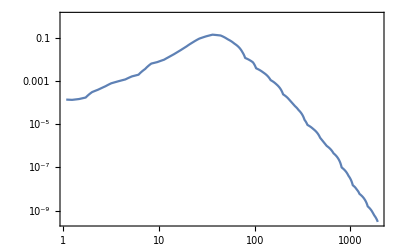

```mathematica
(*****************************)
(* Atomic Ionization Factor *)
(*****************************)
Kdata={{1.068 10^-6,1.394 10^-4},
{1.230 10^-6,1.357 10^-4},
{1.456 10^-6,1.484 10^-4},
{1.708 10^-6,1.743 10^-4},
{1.993 10^-6,3.115 10^-4},
{2.321 10^-6,4.077 10^-4},
{2.747 10^-6,5.787 10^-4},
{3.157 10^-6,7.950 10^-4},
{3.760 10^-6,9.928 10^-4},
{4.435 10^-6,1.204 10^-3},
{5.192 10^-6,1.659 10^-3},
{6.095 10^-6,1.995 10^-3},
{7.152 10^-6,3.678 10^-3},
{8.287 10^-6,6.530 10^-3},
{9.579 10^-6,7.662 10^-3},
{1.129 10^-5,9.911 10^-3},
{1.325 10^-5,1.454 10^-2},
{1.568 10^-5,2.206 10^-2},
{1.887 10^-5,3.725 10^-2},
{2.234 10^-5,6.164 10^-2},
{2.635 10^-5,9.405 10^-2},
{3.096 10^-5,1.195 10^-1},
{3.621 10^-5,1.431 10^-1},
{4.395 10^-5,1.309 10^-1},
{5.196 10^-5,8.821 10^-2},
{6.099 10^-5,5.575 10^-2},
{7.422 10^-5,2.229 10^-2},
{7.937 10^-5,1.192 10^-2},
{9.578 10^-5,7.459 10^-3},
{1.033 10^-4,3.954 10^-3},
{1.222 10^-4,2.562 10^-3},
{1.467 10^-4,1.115 10^-3},
{1.685 10^-4,7.143 10^-4},
{1.980 10^-4,2.443 10^-4},
{2.442 10^-4,8.874 10^-5},
{2.874 10^-4,4.571 10^-5},
{3.316 10^-4,1.613 10^-5},
{3.561 10^-4,9.334 10^-6},
{4.092 10^-4,6.047 10^-6},
{4.909 10^-4,1.972 10^-6},
{5.664 10^-4,9.907 10^-7},
{6.667 10^-4,4.519 10^-7},
{8.109 10^-4,9.966 10^-8},
{9.557 10^-4,4.105 10^-8},
{1.060 10^-3,1.494 10^-8},
{1.246 10^-3,5.929 10^-9},
{1.519 10^-3,1.565 10^-9},
{1.755 10^-3,6.414 10^-10},
{1.936 10^-3,2.975 10^-10}}; (* {GeV, } *)
Kfactor=Interpolation[Kdata,InterpolationOrder->1];
LogLogPlot[Kfactor[q 10^-6],{q,1.068 10^0, 1.936 10^3},Frame->True]
```

```mathematica
qint[Er_,v_]:=NIntegrate[q Kfactor[q],{q ,qmin[Er,v],qmax[Er,v]}];(* GeV^2 *)
```

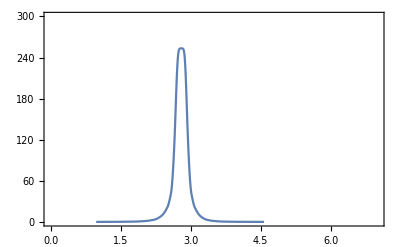

```mathematica
Plot[qint[Er 10^-6,vesc+vE](10^6)^2,{Er,0,7},PlotRange->{{0,7},{0,300}},Frame-> True]
```

```mathematica
(*******************)
(* Scattering Rate *)
(*******************) 
func1[v_]=2π v^2 Integrate[VelDist[v,θ],{θ,-1,1(*(vesc^2-v^2-vE^2)/(2 vE v)*)}] ;
```

```mathematica
rateEnergy[Er_]:=(rhox2 Nt)/mx sigmae/(2 me)a0^2 (light 10^5) (NIntegrate[1/v qint[Er,v]func1[v],{v,vmin[Er],vesc+vE}])10^-6 (60/1 60/1 24/1 365/1) ;   (* yr^-1 ton^-1 KeV^-1 *)
```

```mathematica
ratedata=Table[{i,rateEnergy[i 10^-6]},{i,1,4,(4-1)/100}];
rateEr=Interpolation[ratedata,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
checkdata={{1.043,7.004 10^-1},
{1.107,7.004 10^-1},
{1.171,7.004 10^-1},
{1.236,7.004 10^-1},
{1.300,7.004 10^-1},
{1.364,7.004 10^-1},
{1.429,7.004 10^-1},
{1.493,7.004 10^-1},
{1.557,7.004 10^-1},
{1.622,7.004 10^-1},
{1.686,7.004 10^-1},
{1.750,7.004 10^-1},
{1.815,7.004 10^-1},
{1.879,1.631 },
{1.943,1.631},
{2.008,1.631},
{2.072,1.631},
{2.137,1.631},
{2.201,1.631},
{2.265,1.631},
{2.330,1.631},
{2.394,1.885},
{2.458,3.070},
{2.523,5.693},
{2.587,1.212 10^1},
{2.643,2.723 10^1},
{2.678,5.074 10^1},
{2.698,7.540 10^1},
{2.710,1.045 10^2},
{2.722,1.316 10^2},
{2.727,1.585 10^2},
{2.733,1.955 10^2},
{2.739,2.318 10^2},
{2.745,2.690 10^2},
{2.751,3.191 10^2},
{2.757,3.421 10^2},
{2.760,3.656 10^2},
{2.762,3.931 10^2},
{2.765,4.168 10^2},
{2.771,4.447 10^2},
{2.775,4.685 10^2},
{2.777,4.979 10^2},
{2.784,5.695 10^2},
{2.791,5.993 10^2},
{2.812,5.584 10^2},
{2.817,5.239 10^2},
{2.829,3.945 10^2},
{2.830,4.382 10^2},
{2.835,3.395 10^2},
{2.837,3.675 10^2},
{2.840,2.852 10^2},
{2.842,3.135 10^2},
{2.847,2.558 10^2},
{2.853,2.199 10^2},
{2.862,1.846 10^2},
{2.868,1.496 10^2},
{2.874,1.199 10^2},
{2.879,9.596 10^1},
{2.891,7.284 10^1},
{2.908,4.740 10^1},
{2.944,2.331 10^1},
{2.996,9.248},
{3.061,3.832},
{3.125,1.716},
{3.190,1.631},
{3.254,1.631},
{3.318,1.631},
{3.383,1.124},
{3.447,7.004 10^-1},
{3.511,7.004 10^-1},
{3.576,7.004 10^-1},
{3.640,7.004 10^-1},
{3.704,7.004 10^-1},
{3.769,7.004 10^-1},
{3.833,7.004 10^-1},
{3.897,7.004 10^-1},
{3.962,7.004 10^-1},
{3.997,7.004 10^-1}};
checkfunc=Interpolation[checkdata,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
tPowerTicks[label_][min_,max_]:=Block[{min10,max10},min10=Floor[Log10[min]];
max10=Ceiling[Log10[max]];
Join[Table[{10^i,If[label,Superscript["10",i]]},{i,min10,max10}],Flatten[Table[{k 10^i,Spacer[{0,0}]},{i,min10,max10},{k,9}],1]]];
```

InterpolatingFunction::dmval: Input value {1.00003} lies outside the range of data in the interpolating function. Extrapolation will be used.

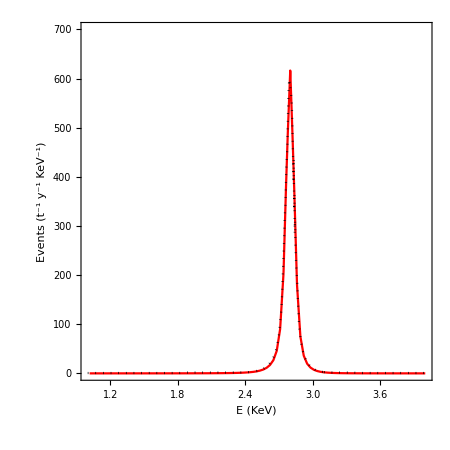

```mathematica
Show[Plot[rateEr[i],{i,1 ,4 },PlotStyle->{Red},PlotRange-> {{ 1 ,4  },{0,700}},FrameTicks-> {{tPowerTicks[True][10^-4, 10^3],Automatic}}],Plot[checkfunc[i],{i,1,2.5},PlotStyle->{Black,Dotted}],Plot[checkfunc[i],{i,2.5,2.8},PlotStyle->{Black,Dotted}],Plot[checkfunc[i],{i,2.8,3.1},PlotStyle->{Black,Dotted}],Plot[checkfunc[i],{i,3.1,4},PlotStyle->{Black,Dotted}],Frame-> True,AspectRatio-> 1,FrameLabel-> { "E (KeV)","Events (t^-1 y^-1 KeV^-1)"},LabelStyle-> Directive[Black,FontSize-> 25],FrameStyle-> Directive[Black,Thickness[0.0035]],ImageSize-> 450]
```